# Mathematica Basics

## Basics

Mathematica is a rich-text mathematics editor - much like Jupyter Notebooks or .mlx files in MATLAB. .nb files can be formatted just like Word documents, where you can mix in equations, executable code, and pictures. 
The number one thing to remember in Mathematica is all built-in functions are Capitalized and take arguments between square brackets [ ]

## A notebook is made from “cells”

Everything in Mathematica from text to input is contained within cells.

Any formatting will apply to the entire cell

Press Shift+Enter to evaluate cell

Press Ctrl+Shift+d to divide cell

Press Alt+Enter to start new cell of the same type

```mathematica
X=0
```

0

## Lists

Mathematica is build on lists. They are the most general structure in Mathematica. You can build them in several ways:

```mathematica
flist = {3,4,5,6,7,8}
slist = List[3,4,5,6,7,8]
rlist = Range[3,8]
rlist2 = Range[3,8,1/4]//N
mixlist = {2,"catch",4,5,True}
```

{3,4,5,6,7,8}

{3,4,5,6,7,8}

{3,4,5,6,7,8}

{3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.}

{2,catch,4,5,True}

You can use indexing to extract elements just as in MATLAB or Python:

```mathematica
flist[[4]]
flist[[2;;5]]
3*flist[[3;;]]
3*mixlist[[2]]
```

6

{4,5,6,7}

{15,18,21,24}

3 catch

You can apply functions directly to list - the functions will return lists :

```mathematica
Sqrt[flist]
Sqrt[flist]//N
Log[flist]//N
```

{√3,2,√5,√6,√7,2 √2}

{1.73205,2.,2.23607,2.44949,2.64575,2.82843}

{1.09861,1.38629,1.60944,1.79176,1.94591,2.07944}

There is a plethora of useful functions you can use to manipulate lists:

```mathematica
v=RandomInteger[{1,50},10]
```

{48,47,14,9,17,36,13,15,13,15}

```mathematica
Sort[v]
Union[v]
Reverse[v]
Prepend[v,4.5]
Append[v,4.5]
Delete[v,6]
```

{9,13,13,14,15,15,17,36,47,48}

{9,13,14,15,17,36,47,48}

{15,13,15,13,36,17,9,14,47,48}

{4.5,48,47,14,9,17,36,13,15,13,15}

{48,47,14,9,17,36,13,15,13,15,4.5}

{48,47,14,9,17,13,15,13,15}

## Import Data

Mathematica can import numerous file formats, including ones produced by other programs. (When importing files, be extra careful with your directory path).

```mathematica
sun = Import["sunspotsbyyear.csv"];
```

Import::nffil: File sunspotsbyyear.csv not found during Import.

It will most likely be imported as a nested list - a list of lists. Use the same syntax to extract elements

```mathematica
sun=Flatten[sun]
sun = Partition[sun,5]
sun[[9]];
sun[[9,2]];
sun[[All,2]];
ListPlot[sun[[All,2]],Joined->True];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Flatten[$Failed]

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

Flatten[]

Part::partw: Part 9 of Flatten[] does not exist.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

ListPlot::lpn: Flatten[] is not a list of numbers or pairs of numbers.

## Defining Functions

There are 3 common ways to define functions in Mathematica

```mathematica
f = Function[{x,y},x^2+y^2];
g = (#1^2+#2^2) &;
h[x_,y_] := x^2+y^2;
f[2,3]
g[2,3]
h[2,3]
```

13

13

13

I do prefer the explicitly definition

h[x_,y_] := x^2+y^2

The := is a delayed assignment operator, meaning that every time you call h, Mathematica will return and redefine the function. This is a very nice option since parameters inside your function definition could change from when it is created to when it is called. For example, try the code below by assigning fun with = and then with :=

```mathematica
a=2;
F[x_]:= (a*x^3)/(Exp[x]-1);
G[x_] = (a*x^3)/(Exp[x]-1);
```

```mathematica
F[2]-G[2]
a=4;
G[2]
```

0

16/(-1+ⅇ^2)

```mathematica
xRange[v_,θ_,h_,g_] := (v^2 Cos[θ] Sin[θ])/g+√((v^4 Cos[θ]^2 Sin[θ]^2)/g^2+(2 h v^2 Cos[θ]^2)/g);
xRange[45,60*π/180,0,9.81]//N
Sqrt[4]+ 6^2
Cos[π]//N
```

178.767

38

-1.

## More Advanced Mathematical Operations

Mathematica’s great advantage over other programming languages is it’s symbolic engine. Mathematica can perform symbolic calculations on almost any analytic expression. Not only that but it can then numerically evaluate those same expressions. Let’s look at some examples:

#### Simple Equation Solving

```mathematica
xsol=Solve[x^3-x-9==0,x]//N
```

```mathematica
xsol=Flatten[xsol]
6*x^2-8*x/.xsol[[1]]//N
```

{x→2.24004,x→-1.12002-1.66233 ⅈ,x→-1.12002+1.66233 ⅈ}

12.1864

#### System of Equations

The classic physics example of a situation requiring a system of equations is simple DC circuits (although, more complex circuits require them too). Let’s look at a circuit like this one:
-Graphics-

Recalling Kirchhoff’s Laws, the system of equations that relate all the currents, voltages, and resistors for this circuit is

V_1 -i_1 R_1-i_2 R_2+V_2-i_1 R_1 = 0
V_2 +i_3 R_1+i_3 R_2+V_3-i_2 R_2 = 0
i_1=i_2+i_3

Coding this into Mathematica,

```mathematica
currents=Solve[{Subscript[V, 1] -Subscript[i, 1] Subscript[R, 1]-Subscript[i, 2] Subscript[R, 2]+Subscript[V, 2]-Subscript[i, 1] Subscript[R, 1] == 0,Subscript[V, 2] +Subscript[i, 3] Subscript[R, 1]+Subscript[i, 3] Subscript[R, 2]+Subscript[V, 3]-Subscript[i, 2] Subscript[R, 2] == 0,Subscript[i, 1]==Subscript[i, 2]+Subscript[i, 3]},{Subscript[i, 1],Subscript[i, 2],Subscript[i, 3]}]//FullSimplify
```

{{i_1→(R_1 (V_1+V_2)+R_2 (2 V_1+V_2-V_3))/(2 R_1^2+5 R_1 R_2+R_2^2),i_2→(R_2 (V_1+V_2)+R_1 (V_1+3 V_2+2 V_3))/(2 R_1^2+5 R_1 R_2+R_2^2),i_3→(R_2 (V_1-V_3)-2 R_1 (V_2+V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)}}

```mathematica
currents2=Flatten[currents]
```

{i_1→(R_1 (V_1+V_2)+R_2 (2 V_1+V_2-V_3))/(2 R_1^2+5 R_1 R_2+R_2^2),i_2→(R_2 (V_1+V_2)+R_1 (V_1+3 V_2+2 V_3))/(2 R_1^2+5 R_1 R_2+R_2^2),i_3→(R_2 (V_1-V_3)-2 R_1 (V_2+V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)}

```mathematica
currents2[[1,2]]
```

(R_1 (V_1+V_2)+R_2 (2 V_1+V_2-V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)

```mathematica
Subscript[i, 1]-Subscript[i, 2]-Subscript[i, 3]/.currents2
Subscript[i, 1]-Subscript[i, 2]-Subscript[i, 3]/.currents2//FullSimplify
```

(R_1 (V_1+V_2)+R_2 (2 V_1+V_2-V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)-(R_2 (V_1-V_3)-2 R_1 (V_2+V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)-(R_2 (V_1+V_2)+R_1 (V_1+3 V_2+2 V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)

0

#### Hydrogen Atom Wavefunction

The wavefunctions for the hydrogen atom are combinations of Laguerre Polynomials and Spherical Harmonic functions, both of which are built-in functions of Mathematica. Here is the wave function for the n=3, l=0, m_l=0 wavefunction:

```mathematica
ψ[r_,ϕ_,θ_] := 1/(81 √(3*π*a^3))(27-18*r/a+2*r^2/a^2)Exp[-r/(3*a)]
Ψ α θ Α ψ Ω ω
D[ψ[r,ϕ,θ],r]//FullSimplify
ψ[2,π/2,π]
```

α Α θ ψ Ψ ω Ω

-(ⅇ^(-r/12) (648+(-60+r) r))/(62208 √(3 π))

37/(1296 ⅇ^(1/6) √(3 π))

```mathematica
Integrate[Integrate[Integrate[ψ[r,ϕ,θ]^2*r^2*Sin[θ],{r,0,a}],{ϕ,0,2*π}],{θ,0,π}]//N
```

0.00986636

You’ll look at the Spherical Harmonic functions in Mathematica_Lesson.nb.

#### Pendulum, small-angle approximation

```mathematica
Clear[g,L]
sol = DSolve[{θ''[t] == -g/L*θ[t],θ[0]==0.03,θ'[0]==0},θ[t],t]
```

{{θ[t]→0.03 Cos[(√g t)/(√L)]}}

```mathematica
sol[[1,1,2]]
```

0.03 Cos[(√g t)/(√L)]

Non-linear Pendulum Problem

```mathematica
g = 9.8;
L = 1;
sol = NDSolve[{θ''[t] == -g/L*Sin[θ[t]],θ[0]==π/2,θ'[0]==0},θ[t],{t,0,20}]
```

{{θ[t]→InterpolatingFunction[…][t]}}

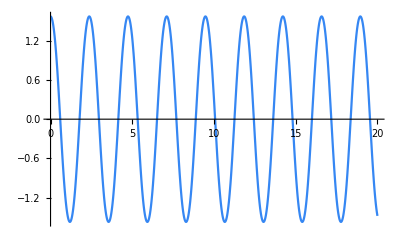

```mathematica
Plot[θ[t]/.sol,{t,0,20}]
```

```mathematica
T[theta0_] := NIntegrate[4*√(L/(2g))1/(√(Cos[θ]-Cos[theta0])),{θ,0,theta0}]
```

```mathematica
T[1.57]
```

2.36862

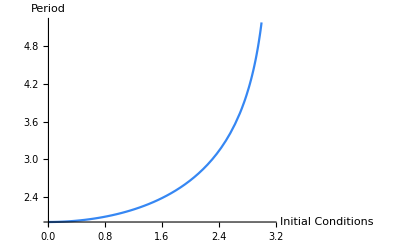

```mathematica
Plot[T[x],{x,0.01,π},AxesLabel->{"Initial Conditions","Period"}]
```